# Unit Triangle

info@cafeplanck.com

```mathematica
UnitTriangle[x]//TraditionalForm
```

x

```mathematica
PiecewiseExpand[UnitTriangle[x]]
```

Piecewise[{{1-x, 0≤x≤1}, {1+x, -1≤x<0}, {0, True}}]

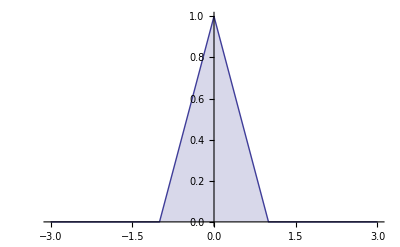

```mathematica
Plot[UnitTriangle[x],{x,-3,3},Filling->Axis]
```

```mathematica
UnitTriangle[x,y]//TraditionalForm
```

x,y

```mathematica
PiecewiseExpand[UnitTriangle[x,y],-3<x<3,-3<y<3]
```

Piecewise[{{(-1+x) (-1+y), 0≤x≤1&&0≤y≤1}, {-(1+x) (-1+y), -1≤x<0&&0≤y≤1}, {-(-1+x) (1+y), 0≤x≤1&&-1≤y<0}, {(1+x) (1+y), -1≤x<0&&-1≤y<0}, {0, True}}]

```mathematica
Plot3D[UnitTriangle[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
∫_(-∞)^(+∞) UnitTriangle[x]ⅆx
```

1

```mathematica
FourierTransform[UnitTriangle[x],x,t]
```

Sinc[t/2]^2/(√(2 π))

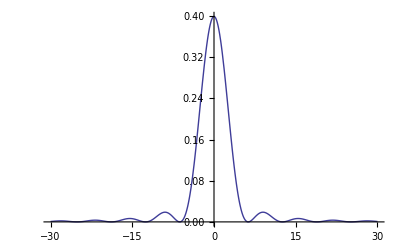

```mathematica
Plot[FourierTransform[UnitTriangle[x],x,t],{t,-30,30},PlotRange->All]
```